```mathematica
ab=0.5291772083; (*Bohr radius in angstroms *)
```

```mathematica
Ry=13.60569172; (*Rydberg energy in eV *)
```

```mathematica
m1=0.2; m2=0.42;  (*Effective electron masses in the quantum dot and matrix,respectively,are given in units of the free electron mass*)
```

```mathematica
U0=2.7/2/Ry; (*2.7 eV is potential energy of confinement. U0 is potential energy of confinement in Hartee units*)
```

```mathematica
h=1; (*Planck constant in Hartree units*)
```

```mathematica
a=40/ab; (*40 Å is the QD radius. a is the QD radius in Hartree units*)
```

```mathematica
L=1/ab;(*0.5 Å is parameter of smooth potential. L is parameter of smooth potential in Hartree units*)
```

```mathematica
U[r_]=U0/2(1+Tanh[(r-a)/L]); (*smooth potential*)
```

```mathematica
(*equation parameters in the QD*)
```

```mathematica
p1[r_]:=0;   λ1[EE_,r_]:=(2*m1)/h^2 EE;   q1[EE_,l_,r_]:=-(l(l+1))/r^2-(2m1)/h^2*(U[r])
```

```mathematica
(*equation for phase in the QD*)
```

```mathematica
eq1[EE_,l_]:=D[φ[r],r]==Cos[φ[r]]^2+p1[r]*Sin[φ[r]]*Cos[φ[r]]+(λ1[EE,r]+q1[EE,l,r])*Sin[φ[r]]^2
```

```mathematica
(*equation's solution which should be calculated*)
```

```mathematica
sol[EE_,l_]:=NDSolve[{eq1[EE,l],φ[0]==0},φ,{r,0,a}]
```

```mathematica
(*solution as a function of energy, quantum number l and coordinate in the QD*)
```

```mathematica
y1[r_,l_,EE_]:=(((φ[r]/.sol[EE,l][[1,1]]))/.r->r)
```

```mathematica
(*A0 is the matrix size. In idel case it is very large*)
```

```mathematica
A0=50a;
```

```mathematica
(*equation parameters in the matrix*)
```

```mathematica
p2[r_]:=0; λ2[EE_,r_]:=(2*m2)/h^2 EE; q2[EE_,l_,r_]:=-(l(l+1))/r^2-(2m2)/h^2*(U[r])
```

```mathematica
(*equation for phase in the matrix*)
```

```mathematica
eq2[EE_,l_]:=D[φ[r],r]==Cos[φ[r]]^2+p2[r]*Sin[φ[r]]*Cos[φ[r]]+(λ2[EE,r]+q2[EE,l,r])*Sin[φ[r]]^2
```

```mathematica
(*equation's solution which should be calculated*)
```

```mathematica
sol2[EE_,l_]:=NDSolve[{eq2[EE,l],φ[A0]==0},φ,{r,a,A0}]
```

```mathematica
(*solution as a function of energy, quantum number l and coordinate in the matrix*)
```

```mathematica
y2[r_,l_,EE_]:=(((φ[r]/.sol2[EE,l][[1,1]]))/.r->r)
```

```mathematica
(*equation for energy finding*)
```

```mathematica
Dysp[EE_,l_]:=Det[({{Sin[y1[a,l,EE]], -Sin[y2[a,l,EE]]}, {1/m1*(-Sin[y1[a,l,EE]]/a^2+Cos[y1[a,l,EE]]/a), -1/m2*(-Sin[y2[a,l,EE]]/a^2+Cos[y2[a,l,EE]]/a)}})]
```

```mathematica
(*s-states l=0*)
```

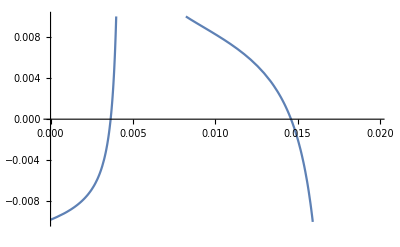

```mathematica
Plot[Dysp[EE,0],{EE,0,U0/5},PlotRange->{-0.01,0.01}]
```

```mathematica
(*solution range*)
```

```mathematica
x1=0.001;x2=0.005;
```

```mathematica
pp=ParallelTable[{i,Dysp[i,0]},{i,x1,x2,10^(-5)}];
```

```mathematica
gr=Interpolation[pp];
```

```mathematica
eq3=FindRoot[gr[EE]==0,{EE,x1,x2}]
```

{EE→0.00364781}

```mathematica
(*energy in meV*)
```

```mathematica
En=eq3[[1,2]]*2*Ry*1000
```

99.262